# Adaptive Morse code recognition using k-means clustering

## Algorithm prototype

This notebook contains a prototype algorithm for adaptive morse code symbol recognition based on k-means clustering, designed with the intent of implementing non-iambic (“straight key”) code recognition on the TI MSP430 LaunchPad — namely, on the MSP430G2553 — and writing decoded symbols out on the microcontroller’s UART.

This application imposes certain constraints, most particularly a need to decode symbols immediately after receipt even at the expense of accuracy (i.e., no lookahead is possible), as well as limitations on math performance and available memory (the MSP430G2553 has only 512 bytes of RAM). The k-means clustering algorithm is a good fit for adaptive interval recognition under these constraints, as it relies on only simple arithmetic and does not impose a large code or memory overhead. However, since we will be running the algorithm against a rolling data set, some modifications are required in order to prevent degenerate behavior.

The “data” subdirectory accompanying this notebook includes a number of example datasets taken by keying the LaunchPad’s pushbutton. Each dataset is represented by a CSV file in which each row represents a key press interval; the first column is the interval’s start time, and the second is the end time. These data sets come already debounced. A corresponding TXT file contains the decoded symbols for the set. Functions included in this notebook provide quantitative analysis of the recognition algorithm’s accuracy by comparing results against the contents of these TXT files.

Mark Shroyer <code@markshroyer.com>
8 April 2013

## Utility functions

The following functions do not implement the morse code recognition algorithm itself, but will be useful for testing and analyzing the performance of the algorithm.

### Data import

Imports the named sample dataset from its CSV file. The data represents individual pushbutton presses; each entry in the first column indicates the time in milliseconds at which the press began, and the second column the time when it ended:

```mathematica
MessageFileName[messageName_,extension_]:=FileNameJoin[{NotebookDirectory[],"data",messageName<>"."<>extension}]
```

```mathematica
ImportMessage[messageName_]:=With[{message=Import[MessageFileName[messageName,"csv"],"CSV"]},
message-Min[message]]
```

```mathematica
ImportText[messageName_]:=Import[MessageFileName[messageName,"txt"]]
```

Constructs a sequence from multiple data sets, separated with (by default) two seconds of silence:

```mathematica
ImportMessages[messageNames_,OptionsPattern[{space->2000}]]:=Module[{result={}},(With[{offset=If[Max[result]>0,Max[result]+OptionValue[space],0]},result=Join[result,ImportMessage[#]+offset]])&/@messageNames;result]
```

```mathematica
ImportTexts[messageNames_]:=StringJoin[Riffle[ImportText/@messageNames," "]]
```

### Visual analysis

Plots a data set for visual analysis of morse code transmissions:

```mathematica
messageWrap=5000;
messageLineHeight = 400;
MillisToPoint[millis_]:={Mod[millis,messageWrap],-Floor[millis/messageWrap]*messageLineHeight}
MarkLine[start_,end_]:=
With[{startPoint=MillisToPoint[start],endPoint=MillisToPoint[end]},
If[startPoint[[2]]==endPoint[[2]],
{Line[{startPoint,endPoint}]},
{Line[{startPoint,{messageWrap,startPoint[[2]]}}],
Line[{{0,endPoint[[2]]},endPoint}]}]]
PlotMessage[message_,OptionsPattern[{marks->{},letters->{}}]]:=With[{endY=MillisToPoint[Max[message]][[2]]-messageLineHeight},Graphics[Join[Flatten[(MarkLine@@#)&/@message,1],
{Blue},Map[(Text[#[[2]],MillisToPoint[#[[1]]]+{0,-50}])&,OptionValue[marks]],
{Red},Map[(Text[#[[2]],MillisToPoint[#[[1]]]+{0,-150}])&,OptionValue[letters]],
{LightGray,Line[{{0,0},{0,endY}}],Line[{{messageWrap,0},{messageWrap,endY}}]}],BaseStyle->{FontSize->16}]]
```

### Error quantification

Functions for quantifying the quality of the algorithm’s output against expected results.

```mathematica
MessageAccuracy[decoded_,expected_]:=N[EditDistance[expected,decoded]/StringLength[expected]]
```

### Miscellaneous

```mathematica
RepeatList[lst_,n_]:=Module[{result={}},Do[result=Join[result,lst],{i,n}];result]
```

## Morse code symbol definitions

Our morse code alphabet:

```mathematica
morseSymbols={{"A",".-"},{"B","-..."},{"C","-.-."},{"D","-.."},{"E","."},{"F","..-."},{"G","--."},{"H","...."},{"I",".."},{"J",".---"},{"K","-.-"},{"L",".-.."},{"M","--"},{"N","-."},{"O","---"},{"P",".--."},{"Q","--.-"},{"R",".-."},{"S","..."},{"T","-"},{"U","..-"},{"V","...-"},{"W",".--"},{"X","-..-"},{"Y","-.--"},{"Z","--.."},{"1",".----"},{"2","..---"},{"3","...--"},{"4","....-"},{"5","....."},{"6","-...."},{"7","--..."},{"8","---.."},{"9","----."},{"0","-----"}};
```

This function looks up a morse code symbol (given as a strings of periods and hyphens), or returns “?” if there is no match:

```mathematica
DecodeSymbol[symbol_]:=With[{match=Select[morseSymbols,#[[2]]==symbol&,1]},
If[Length[match]>0,First[match][[1]],"?"]]
```

## Recognition algorithm

The algorithm for recognition of morse code marks and symbols is given below.

```mathematica
ClassifyIntervals[message_]:=Map[(Append[#,If[#[[2]]-#[[1]]>150,"-","."]])&,message]
```

Given an existing pair of k-means centroids, classifies an interval of the specified duration would represent either a “dit” or a “dah”:

```mathematica
ClassifyMark[centroids_,duration_]:=If[duration>Mean[centroids],"-","."]
```

Recalculates the k-means centroids for an updated interval buffer:

```mathematica
UpdateCentroids[centroids_,intervals_]:=Module[{result=centroids},
Do[result=N[{Mean[Select[intervals,#≤Mean[result]&]],Mean[Select[intervals,#>Mean[result]&]]}],{5}];
result]
```

Classifies an entire message, grouping marks by apparent letter membership. Returns a list of lists, each nested list containing a letter’s marks.

```mathematica
ClassifyMessage[message_]:=Module[{
(* Current k-means centroids for this iteration *)
centroids={100,300},
(* Buffered intervals for centroid calculation *)
intervals=RepeatList[{100,300},5],
(* Resulting classified mark values, grouped into apparent letters *)
resultMarks={},
(* Incoming marks awaiting grouping into new letter *)
curMarks={},
(* End time of previous mark, in milliseconds *)
prevEnd=0},
Map[Function[mark,
With[{start=mark[[1]],end=mark[[2]]},
(* Detect end of previous letter *)
If[ClassifyMark[centroids,start-prevEnd]=="-",
resultMarks=Append[resultMarks,curMarks];
curMarks={}];
With[{markType=ClassifyMark[centroids,end-start]},
curMarks=Append[curMarks,markType];
prevEnd=end];
intervals=Append[intervals[[2;;]],end-start];
centroids=UpdateCentroids[centroids,intervals]]],message];
resultMarks=Append[resultMarks,curMarks];
resultMarks]
```

```mathematica
DecodeMarks[marks_]:=Composition[DecodeSymbol,StringJoin]/@marks
```

```mathematica
DecodeMessage=Composition[DecodeMarks,ClassifyMessage];
```

```mathematica
AnnotateMarksForMessage[message_]:=With[{marks=ClassifyMessage[message]},
Thread[{(N[(#[[1]]+#[[2]])/2])&/@message,Flatten[marks]}]]
```

```mathematica
AnnotateLettersForMessage[message_]:=With[{marks=ClassifyMessage[message]},
With[{letterIndices=Accumulate[Map[Length,marks]]},
Thread[{#[[2]]&/@Part[message,letterIndices],DecodeMarks[marks]}]]]
```

## Example data

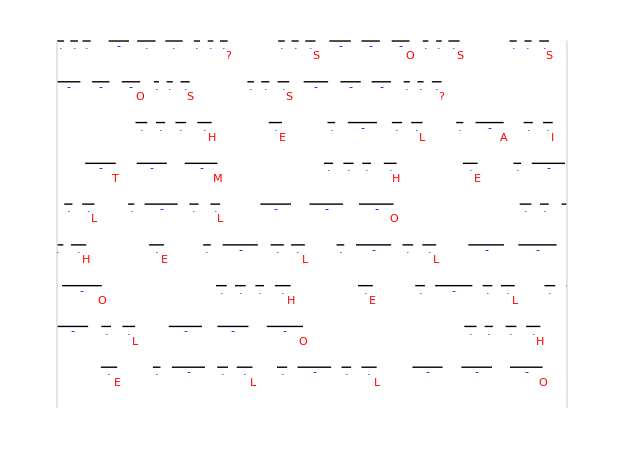

```mathematica
With[{message=ImportMessages[{"sos","hello"}]},
PlotMessage[message,marks->AnnotateMarksForMessage[message],letters->AnnotateLettersForMessage[message]]]
```

## Ideas

### Possible improvements

Lower the threshold for end-of-letter if the marks currently in our buffer form a valid Morse code character

Keep track of borderline mark classifications, and try flipping them if we cannot decode the character

Variations of k-means iteration count

Variations of interval buffer length

Whether or not to preserve centroids when receiving a new mark

If preserving centroids, prevent convergence

Find a way to incorporate the convention that the duration of a dah is three times that of a dit

### Pathological cases to handle

Fill the interval buffer with all dits or all dahs

Discontinuous jump in coding speed resulting in collapse onto a single centriod